```mathematica
Clear[W,M,f,gtable, v,y, x, w12, w13, w23, w34, w21]
```

### Создание графа вычислений

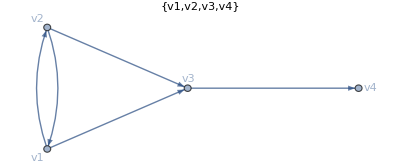
{(0 | 1 | 1 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),-Graphics-}

```mathematica
v={v1,v2,v3,v4}; 
M={{0,1,1,0},{1,0,1,0},{0,0,0,1},{0,0,0,0}};
{MatrixForm[M],AdjacencyGraph[M, VertexLabels->Table[i->v[[i]],{i,1,4}] ,PlotLabel->v, GraphLayout->"SpringElectricalEmbedding"]}
```

Зададим веса связей между элементами в матрице той же размерности, что и матрица связей

```mathematica
W={{0,w12,w13,0},{w21,0,w23,0},{0,0,0,w34},{0,0,0,0}};
MatrixForm[W]
```

(0 | w12 | w13 | 0
w21 | 0 | w23 | 0
0 | 0 | 0 | w34
0 | 0 | 0 | 0)

## Получение значений в вершинах графа после 1-й итерации вычислений

```mathematica
(*  
g(x,W)=f(x.(M*W))=f(y.W')); g:=f(x.W');
 y = g(x, W);
*)
```

```mathematica
y={y1,y2,y3, y4};
x=y.(M*W);
```

Вычисление значений в вершинах

```mathematica
gtable = Table[i->f[x[[i]]],{i,1,Length[x]}] ;(* метки вершин в виде функций*)
```

Метки дуг

```mathematica
edgeslabels=
{
DirectedEdge[1,2]->w12,
DirectedEdge[2,1]->w21,
DirectedEdge[1,3]->w13,
DirectedEdge[2,3]->w23,
DirectedEdge[3,4]->w34
};
```

Визуализация графа и функции

(w21 y2 | w12 y1 | w13 y1+w23 y2 | w34 y3
y1 | y2 | y3 | y4)

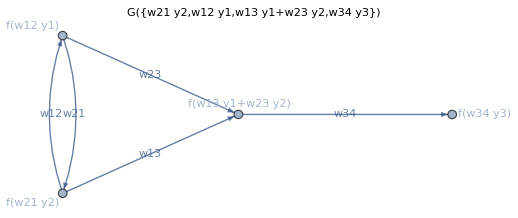

```mathematica
MatrixForm[{x,y}]
AdjacencyGraph[
	M,
	VertexLabels-> gtable,
	DirectedEdges->True,
	PlotLabel->G[x],
	EdgeLabels->edgeslabels,
	GraphLayout->"SpringElectricalEmbedding"]
```

## После определения функций f мы можем вычислить значения в вершинах графа

```mathematica
y={1,-0.1,1.5,0.5};
```

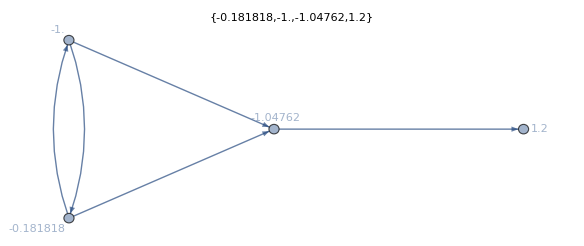

```mathematica
f[x_]:=2*x/(1+Abs[x]);
w12=-1;w13=-1;w23=1;w34=1;w21=1;
x=y.(M*W);
y=f[x];
AdjacencyGraph[M, VertexLabels->Table[i->y[[i]],{i,1,4}] ,PlotLabel->f[x], GraphLayout->"SpringElectricalEmbedding"]
```

## Выполенение нескольких итераций вычислений

```mathematica
nmax=64;
a=2;
f[x_, a_]:= Tanh[x];(* a*x;*)
(*w12=-1;w13=-1;w23=1;w34=1;w21=1;*)
w12=1.1;w21=-1.2;w13=1;w23=1.2;w34=1.1;w41=1;
y={2,0.2,1.5,1.5};
M={{0,1,1,0},{1,0,1,0},{0,0,0,1},{0,0,0,0}};
W={{0,w12,w13,0},{w21,0,w23,0},{0,0,0,w34},{w41,0,0,0}};
Y:=RecurrenceTable[{z[n]==f[z[n-1].(M*W)],z[0]==y},z,{n,1,nmax}];
(*
iter =
Table[
{
n,
AdjacencyGraph[
M, 
VertexLabels->Table[i->Y[[n,i]],{i,1,4}],
GraphLayout->"SpringElectricalEmbedding"]
}, 
{n,1,nmax}
];
TableForm[iter]
*)
a=2;
Manipulate[
AdjacencyGraph[
M, 
VertexLabels->Table[i->Y[[n,i]],{i,1,4}],
GraphLayout->"SpringElectricalEmbedding"
],
{n,1,nmax,1}
]
```